```mathematica
SetDirectory @ NotebookDirectory[];
```

```mathematica
Needs["QuEST`"]
```

```mathematica
env = CreateRemoteQuESTEnv[];
```

LinkConnect::linkc: Unable to connect to LinkObject[55555@igor-gpu.materials.ox.ac.uk,55556@igor-gpu.materials.ox.ac.uk,274,10].

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

```mathematica
env = Install["quest_link"];
```

```mathematica
ψ = CreateQureg[5];
ϕ = CreateQureg[5];
```

```mathematica
InitPlusState[ψ];
InitPlusState[ϕ];
```

```mathematica
u[θ_] := Subscript[Ry, 3][θ] Subscript[C, 3][Subscript[Rz, 2][θ]] Subscript[Ry, 3][θ] Subscript[H, 2] Subscript[X, 3] Subscript[T, 3] Subscript[C, 0][Subscript[X, 1]]
```

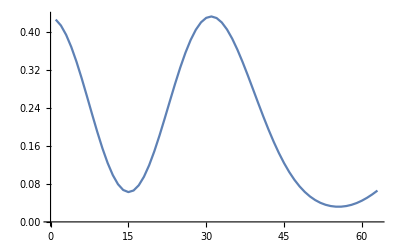

```mathematica
ListLinePlot @  Table[
	CalcFidelity[ψ, ApplyCircuit[u[θ],ψ,ϕ]],
	{θ, 0, 2π, .1}
]
```